# Machine Learning

## Part 2: Generalized Linear Models

Here, we explore the connection between ordinary least squares (OLS), generalized linear models (GLMs), logistic regression (LR), and support vector classification (SVC).  This will prepare us to go on the single-layer perceptron (SLP) in Part 4.

Yen Lee Loh, 2022-12-9

## Section Interpolation versus Fitting

One of the simplest supervised learning problems is curve fitting.  The dataset below, (x_n,y_n) for n=1,2,3,…,N, represents points on the trajectory of a projectile, estimated from a sequence of blurry photos.  We expect that the values of the dependent variable (y_n) are related to the values of the independent variable (x_n) according to y_n=Y(x_n) where Y(x) is a model function.  In the language of machine learning, y_n is a training output  and x_n is an input.  Actually, the model function is Y(x;w) where the vector w={w_1,w_2,…,w_P} contains a set of parameters, whose values we do not yet know.  We would like to find a good choice for w.

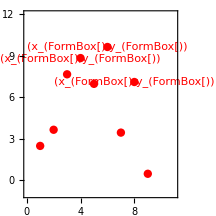
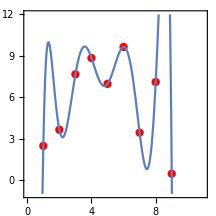
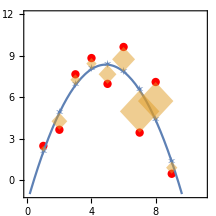
-Graphics- | -Graphics- | -Graphics-
Data | Interpolation | Fit

In an ideal world, we would be able to choose w to make the model match the data exactly, so that y_n=Y(x_n;w) exactly for n=1,2,3,…,N.  This is called interpolation.  To demonstrate this, let us choose a polynomial model Y(x)=c_0+c_1 x+c_2 x^2+…+c_8 x^8.  This model has 9 free parameters, which we can choose to make the curve go through all 9 data points.  However, the figure above shows that the interpolating polynomial exhibits severe overfitting.  It wiggles a lot and lacks physical meaning.

In the real world, we should not strive to obtain a perfect fit (interpolant).  Rather, we should aim for a best fit.  From the viewpoint of Bayesian statistics, to define a best fit, it is not enough for us to have a deterministic model for the output value.  We must have a model for the probability distribution of the output y as a function of the input, P(y_n|x_n), which describes experimental error or factors beyond our control.  In other words, in order to extract the signal accurately, we also need to model the noise.  Based on physical intuition, let choose a quadratic model for the output and a Gaussian model for the noise:
	Y(x)=c_0+c_1 x+c_2 x^2
	p(y|Y)=1/(√(2π σ^2))exp -(y-Y)^2/(2 σ^2).
The probability of the entire dataset is then
	P({y_n}|w)=∏_(n=1)^N p(y_n|Y(x_n)).
The best fit is given by the value of w that maximizes the posterior probability, which is the conditional probability P(w|{y_n}) of the model given the data.  Bayes’ theorem states that the posterior probability is proportional to the prior probability P(w) times the likelihood P({y_n}|w), which is the conditional probability of the data given the model.  If there is a large amount of data, the likelihood will be much more sharply peaked than the prior (as a function of w).  Therefore, to obtain the best fit, we should maximize the likelihood:
	(∂P)/(∂w)=0.
This is called the maximum likelihood principle.

Throughout these notes we will define f=-ln p and F=-ln P to be the cost associated with a probability (also known as loss, penalty, objective function, or criterion).  Here,
  	f(y|Y)= (y-Y)^2						(taking σ=1/√2 and discarding an additive constant),
	F({y_n}|w)=∑_(n=1)^N f(y|Y(x_n))=∑_(n=1)^N [y-Y(x_n)]^2.
Maximizing P is equivalent to minimizing F.  In the present situation, F is the sum of squared differences between the data and the model, and it is often referred to as χ^2 (chi-squared).  Minimizing χ^2 is called applying the method of least squares.  In the figure above, the blue stars are model predictions Y_n=Y(x_n), the red dots are data values y_n, and the area of the orange diamonds is proportional to the squared difference (Y_n-y_n)^2.  The blue curve minimizes the total area of the orange diamonds.

## Section Multivariable Fitting

In the above example, the independent variable x was a single real scalar.  In general, the independent variable may be a vector x.  Then, typically, one chooses a model function for the mean of the dependent variable, Y(x;w), and a model for the probability of fluctuations about that mean, p(y|Y).

As an example, consider the section of the “Titanic” data set below:

"Class" | "Age" | "Sex" | "Result"
1 | 29 | 0 | 1
1 | 1 | 1 | 1
1 | 2 | 0 | 0
1 | 30 | 1 | 0
1 | 25 | 0 | 0
1 | 48 | 1 | 1
1 | 63 | 0 | 1
1 | 39 | 1 | 0
1 | 53 | 0 | 1
1 | 71 | 1 | 0

For each passenger on the doomed ship, the input vector (x_1,x_2,x_3) representing cabin class (1st/2nd/3rd), age, and gender (0=female, 1=male), and the output y is a Boolean variable (0=died, 1=survived).  We might expect that first-class female passengers had a higher probability of survival, and that children and elderly passengers were most vulnerable.  Thus, we might choose a model function Y(x_1,x_2,x_3) with a monotonic dependence on x_1 and x_3 but a possibly non-monotonic dependence on x_2.

## Section Linear Models and Ordinary Least Squares

For many situations, one expects the output to have a monotonic dependence on each input.  Moreover, one expects that the inputs combine approximately additively.  For example, suppose Y is the likelihood of developing cancer and (x_1,x_2,x_3) are variables representing number of cigarettes smoked per day, red meat consumption, and genetic disposition to cancer.  If one has determined that those variables are all risk factors, one might hypothesize that
	Y(x_1,x_2,x_3)=w_1 x_1+w_2 x_2+w_3 x_3=w·x
where x and w are D-dimensional vectors.

Even in the absence of cigarettes, red meat, and oncogenes, there may still be a nonzero probability of cancer.  Therefore one may wish to include a bias term in the model:
	Y(x_1,x_2,x_3)=w_1 x_1+w_2 x_2+w_3 x_3+b.
It is convenient to define a dummy input x_0=1 and a corresponding weight w_0≡b, so that x=(1,x_1,x_2,x_3) and w=(b,w_1,w_2,w_3) are both (D+1)-dimensional vectors.  Then w·x becomes w·x+b.  Throughout these notes, wherever w·x occurs, it may be interpreted as w·x+b.

An ordinary linear model is defined by the predictor(?) function and probability function (“signal” and “noise” functions)
	Y(x|w)=w·x
	p(y|Y)=1/(√(2π σ^2))exp -(y-Y)^2/(2 σ^2).
The probability of the entire dataset is then
	P({y_n}|w)=∏_(n=1)^N p(y_n|Y(x_n|w))=const×∏_(n=1)^N e^(-(y_n-w·x_n)^2)	(taking σ=1/√2)
∴	F({y_n}|w)=∑_(n=1)^N f(y_n|Y(x_n|w))=const+∑_(n=1)^N (y_n-w·x_n)^2.
Thus, we should choose w to minimize F=χ^2.

-Graphics3D-
The figure above shows linear regression applied to a dataset.
The surface shows the mean function Y=w·x+b as a function of (x_1,x_2).
The “water level” on each cone shows where the mean lies on each normal distribution.
The violin plots show normal distributions P∝exp -1/2((y-Y(x_n))/σ)^2 centered on each mean value.
Red bands show sample data points (x_1,x_2,y)_s and where they lie along the respective normal distributions.
If a red band is far above the “water level”, or far below the water level, then it is far from the mean, and it contributes to the cost F.

For a linear model, we may minimize χ^2 analytically to find a closed-form solution for w in terms of {x_n} and {y_n}.  This leads to
	∑_j A_ij w_j=b_i
where A is the covariance matrix of the independent variables, and b is the covariance vector of the dependent variable and independent variables,
	A_ij=Cov_n[x_i,x_j]=1/N∑_(n=1)^N x_ni x_nj,
	b_i=Cov_n[y,x_i]=1/N∑_(n=1)^N y_n x_nj.
This is just a matrix equation.  Therefore we can find a closed-form expression for w:	
	w=⟨x x^T⟩^-1⟨y x^T⟩
where ⟨…⟩ represents the average over all data points n.

## Section Generalized Linear Models

Linear models are not always sufficient.  In the previous example, we might make more complicated hypotheses, such as:
(i) exposure to low levels of cigarette smoke might be harmless, and only becomes harmful above a certain threshold; or
(ii) cigarette smoke accumulates in the lungs causing a compounding effect that increases exponentially with exposure; or
(iii) the number of minutes of exercise per day (x_4) is associated with a decrease in the risk of cancer.
In case (iii), if we write Y(x_1,x_2,x_3,x_4)=w_1 x_1+w_2 x_2+w_3 x_3+w_4 x_4 where w_4<0, this model would predict that lots of exercise will produce a negative risk of cancer, which is unphysical!  Instead, we may wish to write Y(x_1,x_2,x_3,x_4)=exp(w_1 x_1+w_2 x_2+w_3 x_3+w_4 x_4), so that Y can never be negative.

A generalized linear model (GLM) is specified by a combination of a mean function Y(u) and a “spread function” p(y|Y), such that
	P({y_n}|w)=∏_(n=1)^N p(y_n|Y(w·x_n)).

Some of the quantities above have names:
	x					is the input vector
	w					is the weight vector
	u=w·x				is the linear predictor
	Y=Y(u)=Y(w·x)		is the mean prediction
	y					is the target output, training label, or ground-truth value
	p or P				is the likelihood.

It is instructive to visualize a GLM as a flowchart, which will later help us connect GLMs to neural networks:

	x⟶^(linear combination)u⟶^(mean function)Y⟶^(spread function)P.

If Y is the identity function and p(y|Y) is a normal distribution, the generalized linear model reduces to an ordinary linear model.
The infographic below compares several common examples of GLMs.

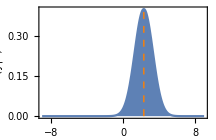
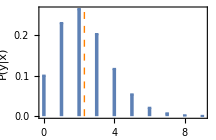
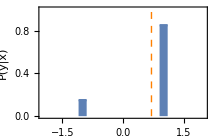
Linear GLM
Mean Y∈(-∞,∞), output y∈(-∞,∞)
Output y normally distributed about mean, Y. 
Finding w is called linear regression or
 ordinary least squares.
	u=w·x
	Y=u
	p=1/(√π)e^(-(y-Y)^2)
Note: σ is arbitrary, and doesn’t affect w. | -Graphics3D- | -Graphics-
Poisson GLM
Mean Y∈[0,∞), output y=0,1,2,…
Output y is Poisson-distributed with mean Y.
	u=w·x
	Y=e^u
	p=(Y^y e^-Y)/(y!) | -Graphics3D- | -Graphics-
Bernoulli GLM
Mean Y∈[-1,1], output y=±1
y is Bernoulli-distributed with mean Y. 
Finding w is called logistic regression.
	u=w·x
	Y=tanh u/2
	p=1/(1+e^-yu)=((1+Y)/2)^((1+y)/2)((1-Y)/2)^((1-y)/2)  | -Graphics3D- | -Graphics-

In the infographic above, the orange surfaces and orange lines represent the mean value Y of the model fit, whereas the blue bars represent the model probability distribution of the actual output value y.  Note that ⟨y⟩=Y in each of the above cases.  See VisualizationsInBayesianStatistics.nb for more detailed illustrations.

A GLM may be thought of a supervised machine learning architecture.  Given training inputs {x_n^train} and training outputs {y_n^train}, we perform the regression to obtain the fit parameters w.  In ML parlance, this is basically “teaching” or “training” the GLM to “learn” the relation between the inputs and outputs.  We can then use the GLM to predict or classify a new set of test inputs {x_n^test}.

## Section Exponential-Poisson Regression

The following dataset represents the activity of a weakly radioactive sample, measured at 1-hour intervals with a 1-second exposure.  We will assume that the radioactive sample contains a large number of nuclei and that the mean number of nuclei decays exponentially as N(t)=N_0 e^-λt, but that the detection efficiency is so low that there are only a few counts within one second.

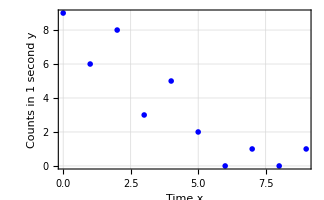

```mathematica
xn={0,1,2,3,4,5,6,7,8,9};
yn={9,6,8,3,5,2,0,1,0,1};
ListPlot[{xn,yn}ᵀ,PlotMarkers->{{"⋆",20}},PlotStyle->Blue,PlotRangePadding->{1,.9},Axes->False,GridLines->Automatic,
FrameLabel->{"Time x","Counts in\n1 second\ny"},ImageSize->{324,192}]
```

We expect the data to lie close to a curve y=A e^-Bx.  Naively, we might write ln y=C-Dx and use linear regression.  However, a typical linear regression routine assumes equal errors σ_(ln y), meaning that σ_y/y is assumed to be the same.  But for counts, one expects σ_y/y∝1/(√y).  Thus, linear regression gives too much weight to data points with small y.

To do better, we can use linear regression with variable weights.  This could still be criticized because linear regression is based on the assumption of Gaussian-distributed fluctuations, whereas the true distribution should be Poissonian, with zero probability of negative counts and with a relatively large tail.

In this situation it makes sense to fit the data with a GLM with an exponential mean function and a Poisson “spread” function:
	u=w·x+b
	Y=e^u
	p=(Y^y e^-Y)/(y!)
	F=∑_(n=1) ln((e^(w·x+b))^y e^(-e^(w·x+b)))/(y!)
[TBD: Do it]

## Section Logistic Regression

Consider the dataset below:

{13.5212,12.1234,19.8864,17.4821,29.866,15.4613,27.734,25.3061,21.0356}

{-1,-1,-1,-1,1,1,-1,1,1}

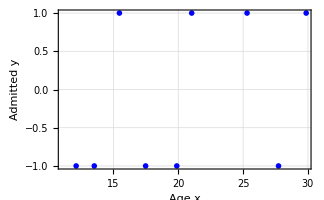

```mathematica
nmax=9;SeedRandom[12345678];
xn=RandomReal[{12,30},nmax]
yn=-1+2RandomVariate[BernoulliDistribution[1/(1+E^(-(#-21)/2.0))]]&/@xn
ListPlot[{xn,yn}ᵀ,PlotMarkers->{{"⋆",20}},PlotStyle->Blue,PlotRangePadding->{1,.9},Axes->False,GridLines->Automatic,
FrameLabel->{"Age x","Admitted\ny"},ImageSize->{324,192}]
```

In the plot above, x_n (n=1,2,3,…,N) are the ages of 9 people who attempted to enter a bar, and y_n=±1 is a Boolean variable that represents whether they were admitted or denied entry.  The legal age is 21, so one would expect that y_n=sgn(x_n-21), but perhaps the bouncer wasn’t checking IDs but merely estimating age from appearance.  We would like to model the carding process, and estimate the probability that a 19-year-old might slip through the cracks.  In the absence of better information, we might assume that the probability of an x-year-old being admitted is Y(x)=1/(1+e^(-(wx+b))), and try to determine w and b as well as we can given the data.  This is called logistic regression.

In logistic regression, we take the mean function to be a tanh function,
	Y(u)=tanh u/2		∈[-1,1]
and the probability function to be a Bernoulli distribution with success probability (1+Y)/2 ∈[0,1].  The Bernoulli distribution is a discrete distribution that is defined only for y=±1.  This allows us to write its probability weight function in many different ways:
	p(y|Y)=((1+Y)/2)^((1+y)/2)((1-Y)/2)^((1-y)/2)       =Piecewise[{{(1+Y)/2, y=+1}, {(1-Y)/2, y=-1}}]   =(1+Y)/2 δ_(y-1)+(1-Y)/2 δ_(y+1)=(1+yY)/2   (if y=±1).
We prefer the first notation because it can be straightforwardly generalized to situations where y is a real number in [-1,1] instead of a Boolean variable.  This may be useful if the training outputs themselves are uncertain (e.g., if there is an unconfirmed allegation that a 19-year-old was found inside the bar).  Substituting Y→tanh u/2, we obtain
	p(y|u)=1/(1+e^-yu)                            =1/2+1/2 tanh u/2=Piecewise[{{1/(1+e^-u), y=+1}, {1/(1+e^u), y=-1.}}]
We prefer the first notation.

In terms of the inputs themselves x, from u=w·x we obtain
	Y=tanh (w·x)/2
	P(y|x)=1/(1+e^(-yw·x)).
The likelihood of an entire dataset is
	P({y_n}|{x_n};w)=∏_(n=1)^N 1/(1+e^(-y_nw·x_n)).
Define f=-ln p and F=-ln P.  Then
	f(y|Y)=(1+y)/2 ln 2/(1+Y)+(1-y)/2 ln 2/(1-Y)
	F(y|x)=ln (1+e^(-yw·x))
	F({y_n}|{x_n};w)=∑_(n=1)^N ((1+y_n)/2 ln 2/(1+Y_n)+(1-y_n)/2 ln 2/(1-Y_n))=∑_(n=1)^N ln (1+e^(-y_nw·x_n)).
Maximizing the overall likelihood is equivalent to minimizing the total cost F.  Above, f is often known as the binary cross-entropy (BCE) function.

For an (ordinary) linear model the mode (most likely prediction) equals the mean (average prediction).  For logistic regression (a tanh+Bernoulli GLM), this is not so.  The most likely prediction is
	Y_mp=sgn Y=sgn u=sgn w·x.

Here is a flowchart to help organize the information:

	input               linear predictor         mean                 probability                                           cost
	x⟶^(linear combination)u⟶^(mean function)Y⟶^(spread function)p ⟶^(log                                          .08) f
	                                     u=w·x                Y=tanh u/2          p=((1+Y)/2)^((1+y)/2)((1-Y)/2)^((1-y)/2)
   =1/(1+e^-yu)          f=(1+y)/2 ln 2/(1+Y)+(1-y)/2 ln 2/(1-Y)
  =ln (1+e^-yu)

Below we visualize Y, p, and f.

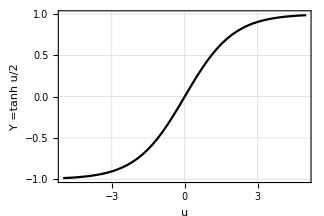

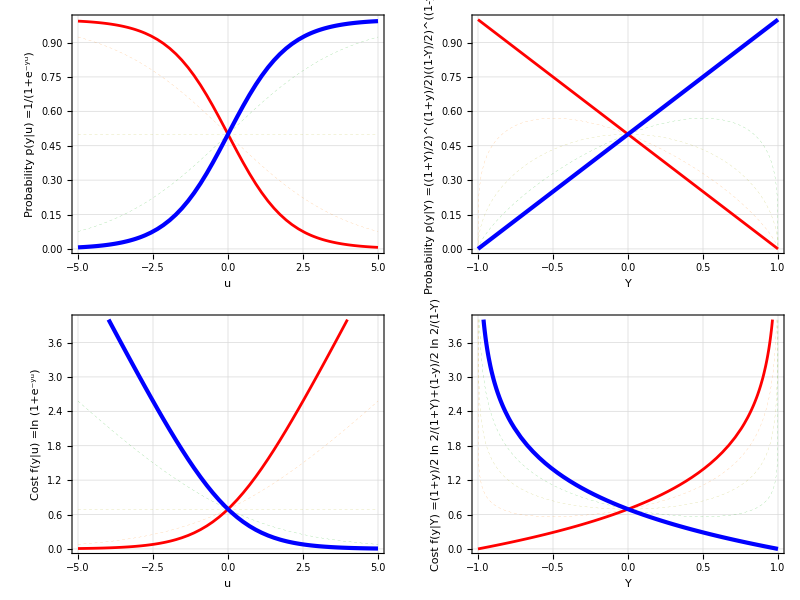

Consider the case y=1.  This corresponds to the thick blue curve in each figure.  
(Top left)  The probability of obtaining y=1 is a sigmoid function of the linear predictor u.
(Bottom left)  If the output is y=1, the cost is 0 if u≫1, whereas the cost is large if u≪-1.  Basically, the function f(y|w·x)=f(yw·x)=ln (1+e^(-yw·x)) is the misclassification penalty.  If w·x>0, then we expect y>0 by a considerable amount.  If y<0 then the log likehood is reduced by a loss function that is approximately linear in y. 
(Top right)  The probability of obtaining y=1 is linearly related to the mean, Y, of the symmetric Bernoulli distribution.
(Bottom right)  If the output is y=1, the cost is f=0 if Y=1, but f->∞ as Y->0.  In other words, a model is not rewarded for predicting the correct answer, but is severely penalized if it confidently predicts the wrong answer.

To perform logistic regression we wish to minimize F.  We cannot solve (∂F)/(∂w)=0 in closed form.  We can minimize F numerically using brute-force methods (simulated annealing, simplex), gradient methods (steepest descent conjugate gradient), or quadratic trust-region methods (Newton, Levenberg-Marquardt, BFGS, DFP).  This is a fairly easy optimization problem because F is a convex function of w that has a single minimum.

Once we have performed the logistic regression to obtain w, we may use the model as follows.

1.  We may evaluate the likelihood of the training data set itself (goodness-of-fit).
2.  We may validate the model on a validation data set (to assess its generalization ability).
3.  Given a single test input x, we may use the model to:
	a.  Obtain the output probability distribution, P(y|x)=1/(1+e^(-yw·x)) where y=±1.
	b.  We may ask the model to predict the mean value of the output, Y=tanh (w·x)/2.
	c.  We may generate a random output (“by hand”) from the output probability distribution, Y_gen=-1 or +1.
	d.  We may ask the model to predict the most likely output, Y_ml=sgn w·x.  (This is called the decision function.)

In (3d), the predicted output is a binary variable, so the prediction is referred to as binary classification.

## Section Support Vector Classification

A support vector machine is a model for support vector classification (SVC).  It is very similar to logistic regression, except that the cost function is defined directly as the hinge loss function applied.08to the linear predictor:
	f(y|u)=ramp(1-yu)=max(0,1-yu)=(1-yu)Θ(1-yu)=Piecewise[{{1-yu, yu<=1}, {0, yu>=1.}}]

The figure below compares the cost function for logistic regression (blue) to that for SVM (orange).

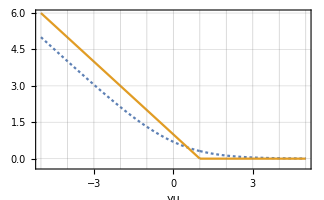

```mathematica
Plot[{
Log[1+Exp[-ywx]],
(1-ywx)UnitStep[1-ywx]
},{ywx,-5,5},PlotStyle->{AbsoluteDashing@2,Solid},PlotLegends->{"f_LR=ln (1+e^-yu)","f_SVC=ramp (1-yu)"},
FrameLabel->{"yu"},PlotRangePadding->{0,0.5},GridLines->{Range[-9,9],Automatic},PlotRange->{All,{-.3,6}},PlotRangePadding->0,AxesOrigin->{0,0}]
```

We may formulate SVC as a GLM with the following flowchart:

Here is a flowchart to help organize the information:

	input               linear predictor         mean                 probability                                           cost
	x⟶^(linear combination)u⟶^(mean function)…⟶^(spread function)p ⟶^(log                                          .08) f
	                                     u=w·x                                                 p∝e^(-ramp(1-yu))                            f=ramp(1-yu)

The plots below show the probability and cost for a SVC model.

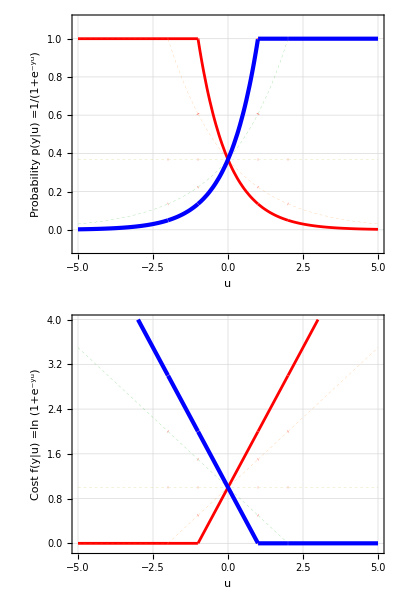

In the bottom panel above, the blue line corresponds to a situation where the correct class is y=+1.   If u>1 then the machine is happy and nothing happens.  If u<=1, the cost is finite, and the machine will try to adjust its weights to increase u.

The model probability distribution, p(y|u)∝e^(-ramp(1-yu)), is rather contrived.  The mean of this distribution is
	Y(u)=⟨y⟩=(∑_(y=±1) y p(y|u))/(∑_(y=±1) p(y|u))=(e^(-ramp(1-u))-e^(-ramp(1+u)))/(e^(-ramp(1-u))+e^(-ramp(1+u)))=Piecewise[{{tanh u, |u|<=1}, {(1-2/(1+e^(1+|u|)))sgn u, |u|>=1}}]		(??)
This is a sigmoid-like function with kinks at u=±1:

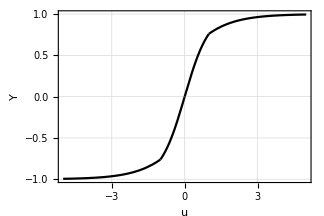
Y=Piecewise[{{tanh u, |u|<=1}, {(1-2/(1+e^(1+|u|)))sgn u, |u|>=1}}] | -Graphics-

In practical use cases, we are not interested in the mean, but only in the mode.  The decision function for SVC is the same as for LR:
	Y_mp=sgn u.

Disadvantage of SVMs:  The model probability distribution is artificial, not based on fundamental physical principles, and is not analytic everywhere (it has a kink).

Advantage of SVMs:  The hinge loss function f=ramp(1-yu) is very simple, which allows f and its derivatives to be computed very quickly.  In addition, because f=0 for points that are on the correct side of the classification margin, those data points don’t even contribute to the loss.  During the bulk of the calculation, the SVM only needs to consider data points within the margin and outliers on the wrong side of the margin.  This allows SVMs to be optimized quickly.

Training data:			x_ni,y_n
Model parameters:		w_i			(weights, including bias term)

## Section Summary

LR (symmetric version)
	P(y|x)=1/(1+e^(-yw·x))				p(y|Y)=e^-bce
	F(y|x)=ln(1+e^(-yw·x))			f(y|Y)=bce
	Y=tanh (w·x)/2
	Y_mp=sgn w·x
	
SVC (symmetric version)
	P(y|x)=e^(-ramp(1-yw·x))
	F(y|x)=ramp(1-yw·x)
	Y=Piecewise[{{1-2/(1+ⅇ^(w·x-1)), w·x≤-1}, {tanh w·x, |w·x|≤1}, {1-2/(1+ⅇ^(w·x+1)), w·x≥1.}}]
	Y_mp=sgn w·x




LR (nonnegative) version?
SVC [0,1] version?

## Appendix: Graphics

### Section.Subsection Interp

```mathematica
SeedRandom[123];
Clear[x,y,interp,fit];
xn={1,2,3,4,5,6,7,8,9};
yn={0,4,7,9,10,9,7,4,0}+2.0*RandomVariate[NormalDistribution[],9];
data={xn,yn}ᵀ;
interp=InterpolatingPolynomial[data,x]//Expand
fit=Fit[data,{1,x,x^2},x]
Yn=fit/.x->xn;
Clear[x,y,Y];
nmax=Length@xn;
{xmin,xmax}={0,11};
{ymin,ymax}={-1,12};
myBlue=ColorData[97][1];
myRed=Red;
myOrange=ColorData[97][2];
opts={PlotRange->{{xmin,xmax},{ymin,ymax}},PlotRangePadding->0,PlotRangeClipping->True,Axes->False,Frame->True,FrameStyle->Black,RotateLabel->False,ImageSize->{216,216},AspectRatio->Full};
grData=Graphics[{myRed,AbsolutePointSize@6,Point/@Transpose@{xn,yn}ᵀ},opts];
grAnnotations=Graphics[{myRed,Table[Text[StringForm["(x_(``),y_(``))",n,n],{xn[[n]],yn[[n]]},{0,-2}],{n,{4,6,8}}]},opts];
grInterp=Plot[interp,{x,xmin,xmax},opts//Evaluate];
grFitCurve=Plot[fit,{x,xmin,xmax},opts//Evaluate];
grFitMarkers=Graphics[{myBlue,AbsolutePointSize@6,Text["✶",#]&/@Transpose@{xn,Yn}ᵀ}];
grLosses=Graphics[{Opacity@.5,myOrange,fac=.4;
Table[
{x,y,Y}={xn[[n]],yn[[n]],Yn[[n]]};ya=(Y+y)/2;xd=Abs[Y-y]*fac;Polygon[{{x,Y},{x+xd,ya},{x,y},{x-xd,ya}}]
,{n,nmax}]
}];
Row@{
Show[grData,grAnnotations],
Show[grData,grInterp,opts],
Show[grData,grFitCurve,grFitMarkers,grLosses,opts]
}
```

-449.71+1215.54 x-1287.36 x^2+713.715 x^3-229.01 x^4+44.0035 x^5-4.98759 x^6+0.307058 x^7-0.00790727 x^8

-1.60116+4.07384 x-0.41627 x^2

-Graphics--Graphics--Graphics-

### Section.Subsection LR

```mathematica
Clear[y,Y];
p[Y_,y_]:=Exp[(1+y)/2 Log[(1+Y)/2]+(1-y)/2 Log[(1-Y)/2]];
f[Y_,y_]:=(1+y)/2 Log[2/(1+Y)]+(1-y)/2 Log[2/(1-Y)];
pu[u_,y_]:=1/(1+Exp[-y*u]);
fu[u_,y_]:=Log[1+Exp[-y*u]];

yList={-1,-.5,0,.5,1};
colors={Directive[AbsoluteThickness@2,Red],Directive[AbsoluteThickness@0,AbsoluteDashing@2,Orange],Directive[AbsoluteThickness@0,AbsoluteDashing@2,Darker@Yellow],Directive[AbsoluteThickness@0,AbsoluteDashing@2,Darker@Green],Directive[AbsoluteThickness@3,Blue]};

gr0=LineLegend[colors,StringForm["TraditionalForm`y = ``",#]&/@yList,LegendLayout->"Row"];
opts={GridLines->Automatic,Axes->None,PlotRangePadding->0,PlotStyle->colors,ImageSize->{324,216},ImagePadding->{{160,4},{48,4}},AspectRatio->Full};
```

```mathematica
Plot[Tanh[u/2],{u,-5,5},PlotStyle->Black,FrameLabel->{"u","Y
=tanh u/2"},PlotRange->{-1,1},Evaluate@opts]
```

-Graphics-

```mathematica
gr1=Plot[Evaluate@Table[p[Y,y],{y,yList}],{Y,-1,1},PlotRange->{{-1,1},{0,1}},
FrameLabel->{"Y","Probability
p(y|Y)
=((1+Y)/2)^((1+y)/2)((1-Y)/2)^((1-y)/2)"},
Evaluate@opts];
gr2=Plot[Evaluate@Table[f[Y,y],{y,yList}],{Y,-1,1},PlotRange->{{-1,1},{0,4}},
FrameLabel->{"Y","Cost
f(y|Y)
=(1+y)/2 ln 2/(1+Y)+(1-y)/2 ln 2/(1-Y)"},
Evaluate@opts];
gr3=Plot[Evaluate@Table[pu[u,y],{y,yList}],{u,-5,5},PlotRange->{All,{0,1}},
FrameLabel->{"u","Probability
p(y|u)
=1/(1+e^-yu)"},
Evaluate@opts];
gr4=Plot[Evaluate@Table[fu[u,y],{y,yList}],{u,-5,5},PlotRange->{All,{0,4}},
FrameLabel->{"u","Cost
f(y|u)
=ln (1+e^-yu)"},
Evaluate@opts];
Column@{gr0,Grid@({{gr3, gr1}, {gr4, gr2}})}
```

-Graphics-

### Section.Subsection SVC

```mathematica
Sum[y*E^(-(1-y u)UnitStep[1-y u]),{y,{-1,1}}]/Sum[1*E^(-(1-y u)UnitStep[1-y u]),{y,{-1,1}}]//PiecewiseExpand//FullSimplify
```

Piecewise[{{1-(2 ⅇ)/(ⅇ+ⅇ^u), u<-1}, {1-2/(1+ⅇ^(1+u)), u>1}, {Tanh[u], True}}]

```mathematica
Clear[y,Y];
pu[u_,y_]:=Exp[-Ramp[1-y*u]];
fu[u_,y_]:=Ramp[1-y*u];

yList={-1,-.5,0,.5,1};
colors={Directive[AbsoluteThickness@2,Red],Directive[AbsoluteThickness@0,AbsoluteDashing@2,Orange],Directive[AbsoluteThickness@0,AbsoluteDashing@2,Darker@Yellow],Directive[AbsoluteThickness@0,AbsoluteDashing@2,Darker@Green],Directive[AbsoluteThickness@3,Blue]};

gr0=LineLegend[colors,StringForm["TraditionalForm`y = ``",#]&/@yList];
opts={GridLines->Automatic,Axes->None,PlotRangePadding->0,PlotStyle->colors,ImageSize->{324,216},ImagePadding->{{108,4},{48,4}},AspectRatio->Full};
```

```mathematica
Plot[Tanh[u]UnitStep[1-u^2]+(1-2/(1+E^(1+Abs[u])))Sign[u]UnitStep[u^2-1],{u,-5,5},PlotStyle->Black,FrameLabel->{"u","Y"},PlotRange->{-1,1},Evaluate@opts]
```

-Graphics-

```mathematica
gr3=Plot[Evaluate@Table[pu[u,y],{y,yList}],{u,-5,5},PlotRange->{All,{-.1,1.1}},
FrameLabel->{"u","Probability
p(y|u)
=1/(1+e^-yu)"},
Evaluate@opts];
gr4=Plot[Evaluate@Table[fu[u,y],{y,yList}],{u,-5,5},PlotRange->{All,{-.1,4}},
FrameLabel->{"u","Cost
f(y|u)
=ln (1+e^-yu)"},
Evaluate@opts];
Row@{gr0,Grid@({{gr3}, {gr4}})}
```

-Graphics-

## Initialization cells

### Section.Subsection Basics

```mathematica
Solid=Dashing@{};
DarkGreen=Darker[Green,0.67];
resistorColorList={Black,Brown,Red,Orange,Darker@Yellow,Darker@Green,Blue,Purple,Gray,Cyan};
resistorStyle[n_Integer]:={AbsoluteThickness@1,resistorColorList[[Mod[n,Length@resistorColorList,1]]]};
purpleWhite[v_]:=Hue[0.75,0.25,Abs[v]^0.5];
blueWhiteRed[v_]:=Hue[If[v>0.5,0.0,0.5],(2Abs[v-0.5]),0.95];
colorFromComplex[z_,OptionsPattern[{Brightness->1.}]]:=Hue[Rescale[Arg@z,{0,2 π}],0.8,1-1/(1+Abs[z*OptionValue[Brightness]])];
enlargeFont=#/.s_String->Style[s,16]&;
myCF=Blend[{
Hue[0.8,0.75,0.75],
Hue[0.7,0.75,0.80],
Hue[0.6,0.75,0.90],
Hue[0.6,0.25,1.00],
White,
RGBColor[0.9938925000000001,0.989345,0.5766145],
RGBColor[0.955963,0.863115,0.283425],
RGBColor[0.881316,0.5539655,0.2226795],
RGBColor[0.817319,0.134167,0.164218]},
Clip[#,{0,1}]]&;
myCF=Blend[{
Hue[0.67,0.75,0.80],
White,
Hue[.15,.75,.80]},
Clip[#,{0,1}]]&;
```

```mathematica
myGS={BaseStyle->{14,FontFamily->"Times",Black}};
myPS={LabelStyle->{14,FontFamily->"Times",Black},ImageSize->324,RotateLabel->False,Frame->True,FrameStyle->Directive@{AbsoluteThickness@0,Black},ImageMargins->1};
myPS1={PlotStyle->ColorData[97]};
SetOptions[Graphics,myGS];
SetOptions[Plot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ParametricPlot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ListPlot,myGS,myPS,myPS1];
SetOptions[ListLinePlot,myGS,myPS,myPS1];
SetOptions[ListLogPlot,myGS,myPS];
SetOptions[ListLogLogPlot,myGS,myPS];
SetOptions[ListLogLinearPlot,myGS,myPS];
SetOptions[DiscretePlot,myGS,myPS];
SetOptions[RectangleChart,myGS,myPS];
SetOptions[ArrayPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[ContourPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[DensityPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[StreamPlot,myGS,myPS,AspectRatio->Automatic,StreamColorFunction->None,StreamStyle->AbsoluteThickness@1];
SetOptions[Graphics3D,PlotRange->All,ImageSize->600,ViewPoint->{-1,-2,1},ViewVertical->{0,0,1},Lighting->"Neutral",Boxed->False,AspectRatio->Automatic];
```

### Section.Subsection Dimension lines (relatively new code: 2021-2-16)

```mathematica
(*---- USER MAY WANT TO TWEAK ARROWSIZE ----*)
dimLine[r1_,r2_,label_,tickLen_,arrowOffset_,labelOffset_]:=Module[{p,u,v,w,
arrowSize=0.015,
grAH=
Graphics[Line@{{-1,.3},{0,0},{-1,-.3}}]
(*Graphics[Polygon@{{-1,.5},{0,0},{-1,-.5}}]*)
},
p=r2-r1;u=Normalize@{-p⟦2⟧,p⟦1⟧};p=Normalize@p;
(*-------- CHECK IF DIMENSION IS SUFFICIENTLY LARGE --------*)
If[
Norm[r2-r1]>.8    (*5Max[tickLen,arrowOffset,labelOffset]*)
,
(*-------- ORDINARY INTERIOR DIMENSION LINE --------*)
{
Arrowheads[{{-arrowSize,Automatic,grAH},{arrowSize,Automatic,grAH}}],Arrow@{r1+arrowOffset*u,r2+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
},
(*-------- SPECIAL EXTERIOR DIMENSION LINE --------*)
{
exteriorLength=1;
Arrowheads[{{arrowSize,Automatic,grAH}}],
Arrow@{r2+exteriorLength*p+arrowOffset*u,r2+arrowOffset*u},
Arrow@{r1-exteriorLength*p+arrowOffset*u,r1+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
}
]
];
groundSymbol[{x_,y_},s_]:=(
Line@{{{0,3},{0,6}},{{-3,3},{3,3}},{{-2,2},{2,2}},{{-1,1},{1,1}}}
)//Translate[#,{0,-6}]&//Scale[#,s,{0,0}]&//Translate[#,{x,y}]&;
```

### Section.Subsection myFormat

```mathematica
(*-------- Pretty-print any real number --------*)
myFormat[v_]:=(
Which[
(*---- If v is an exact power of 10 with an exponent less than -4 or greater than +4, display v as 10^w ----*)
v>0&&Abs@Log10@v>5&&FractionalPart[Log10@v]==0,SuperscriptBox[10,Round@Log10@v],
(*---- If v is an integer, display v without any decimal points ----*)
Abs[v-Round@v]<10^-8,Round@v,
(*---- If v is not an integer, display v with decimals and possibly in scientific notation ----*)
True,NumberForm[N@v,ExponentFunction->(If[-4<#<4,Null,#]&),NumberPoint->"."]
](*//Style[#,FontWeight->Bold]&*));
```

### Section.Subsection Axis utilities: divisions, etc.

Let v be the numerical part of a physical quantity, and let x be the coordinate along the axis on which this quantity is plotted.
For example, suppose we are displaying 200 GHz at coordinate 8.3.  Then v=200×10^11 and x=8.3.
We will supply a conversion function vfromx to the myAxis function.

```mathematica
(*-------- Plotting parameters --------*)
maxMajorDivisions=30;
maxMinorDivisions=300;
tickLengthMajorP=0.25;
tickLengthMajorM=0.;
tickLengthMinorP=0.15;
tickLengthMinorM=0.;
textOffset=1.5;
(*-------- Round up or down to closest number in a list --------*)
roundUp[x_,xlist_]:=Min@Select[xlist,#≥x&];
roundDn[x_,xlist_]:=Max@Select[xlist,#≤x&];
(*-------- Round up or down to the nearest number of the form 1×10^n, 2×10^n, or 5×10^n --------*)
roundUpNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundUp[x/10^expon,{1,2,5,10}]*10^expon];
roundDnNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundDn[x/10^expon,{1,2,5,10}]*10^expon];
(*-------- Divide an interval to find a nice set of tick values --------*)
divisions[{vmin_,vmax_},maxDivisions_]:=Module[{vrange,vstep,vstart,lmin,lmax,v,divs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxDivisions];
vstart=vstep*Ceiling[vmin/vstep];
divs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
Return@divs;
];
(*-------- Divide an interval to find nice major and minor tick values --------*)
divisions[{vmin_,vmax_},{maxMajorDivisions_,maxMinorDivisions_}]:=Module[{vrange,vstep,vstart,lmin,lmax,v,majDivs,minDivs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxMajorDivisions]; (* major division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
majDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
vstep=roundUpNicely[vstep/maxMinorDivisions]; (* minor division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
minDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
minDivs=Complement[minDivs,majDivs];
Return@{majDivs,minDivs}];
(*-------- Divide an interval with major ticks as 10^n and minor ticks as {2,3,4,5,6,7,8,9}×10^n --------*)
(*-------- This works well except when we have a very small interva --------*)
logDivisions[{vmin_,vmax_}]:=Module[{lmin,lmax,v,majDivs,minDivs}, (* l===Log10[v] *)
lmin=Floor@Log10@vmin;
lmax=Ceiling@Log10@vmax;
majDivs=Table[v=10^l;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax}]//Reap//Last//Last;
minDivs=Table[v=10^l*mantissa;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax},{mantissa,2,9}]//Reap//Last//Last;
Return@{majDivs,minDivs}];
linScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=divisions[{vmin,vmax},{30,6}];
vlist2=Flatten@vlist2;
Graphics[{
(*-------- Draw axis line and axis label --------*)
Text[label,{xmin,0},{2.00,0}],
{Line@{{xmin,0},{xmax,0}}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
logScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=Quiet@InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=myLogDivisions[{vmin,vmax}];vlist2=Flatten@vlist2;
(*-------- Draw axis line and axis label --------*)
Graphics[{
Text[label,{xmin,0},{2.00,0}],
Line@{{xmin,0},{xmax,0}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,N@vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
mark[x_,label_]:=Module[{},
{Line@{{x,-10},{x,-.5}},
Text[label,{x,-.5}]}
];
 stackScales[grList_]:=Module[{nmax=Length@grList},
Graphics[{
Table[
(*Inset[grList⟦n⟧,{0,-n}]*)
Translate[grList⟦n⟧⟦1⟧,{0,-n}]
,{n,nmax}],
},
ImageSize->{1200,50*nmax},AspectRatio->Full,
PlotRange->{All,{-nmax-.7,-.1}}
]
]
makeLabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=myFormat},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
makeUnlabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=Null&},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
```

### Section.Subsection autoTicksLabeled, etc.

```mathematica
decimalExponent[x_]:=Floor@Log10[x];
decimalMantissa[x_]:=x/(10^Floor@Log10[x]);
roundUpNicely[x_]:=SelectFirst[{1,2,5,10},#≥decimalMantissa[x]&]*10^decimalExponent[x];
divisions[{xmin_,xmax_},xstep_]:=Range[Ceiling[xmin,xstep],xmax,xstep]//Select[#,xmin≤#≤xmax&]&;
```

```mathematica
autoTicks$TickColor=White; (* MAY NEED TO SET THIS THING *)
autoTicksLabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,myFormat@N@#,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoTicksUnlabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoContours=Function[{zmin,zmax},FindDivisions[{zmin,zmax},50]];
```

### Section.Subsection timeIt

```mathematica
SetAttributes[timeIt,HoldAll];
timeIt[cmds_]:=Module[{report,absTime,cpuTime},
report=AbsoluteTiming[Timing[cmds;]];
absTime=report⟦1⟧;
cpuTime=report⟦2,1⟧;
Print[StringForm["Absolute time = ``    CPU time = ``",absTime//DecimalForm[#,3]&,cpuTime//DecimalForm[#,3]&]]
];
```

### Section.Subsection myRealPlot and myComplexPlot

```mathematica
myRealPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

```mathematica
myComplexPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```